# Clip

info@cafeplanck.com

```mathematica
Clip[x]//TraditionalForm
```

Clip[x]

```mathematica
PiecewiseExpand[Clip[x],-3<x<3]
```

Piecewise[{{-1, x<-1}, {1, x>1}, {x, True}}]

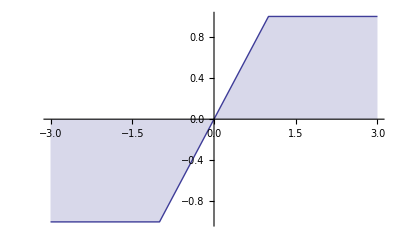

```mathematica
Plot[Clip[x],{x,-3,3},Filling->Axis]
```

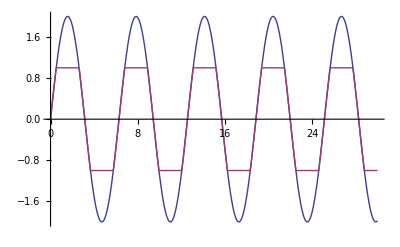

```mathematica
Plot[{2Sin[x],Clip[2 Sin[x]]},{x,0,30}]
```